# The damped driven pendulum

We briefly examined a damped, sinusoidally driven pendulum in lecture 7.  With no driving or damping, it is just a pendulum.  With damping, it behaves in a very simple fashion - particularly over a long timescale.  Adding different strengths and frequencies of driving leads to potentially very complicated behaviour.
   
Here we give you pre - written code to play with this system.  What can you say about how the system behaves?

```mathematica
Unprotect[Equal];
Equal[a_List,b_List]:=If[Length@a≠Length@b,False,Table[a[[j]]==b[[j]],{j,1,Length[a]}]]
Protect[Equal];

r[t_]:={θ[t],pθ[t]}  (* So our variables are just the angle and its momentum *)

solutionPumpedDamped[θ0_,pθ0_,a_,ω_,b_,tmax_]:=NDSolve[{θ'[t]==pθ[t]/m,pθ'[t]==a Sin[ω t]-m g Sin[θ[t]]-b pθ[t],r[0]=={θ0,pθ0}}/.{m->1,g->1},r[t],{t,0,tmax},MaxSteps->100000,Method->"ImplicitRungeKutta"]
```

## Templates for making plots:

Perhaps you wish to simply plot the behaviour as a function of time

```mathematica
Manipulate[ParametricPlot[Evaluate[{θ[t],pθ[t]}/.solutionPumpedDamped[θ0,pθ0,a,ω,b,tmax]],{t,0,tmax},PlotRange->{{-4π L,4π L},{-5,5}},ImageSize->Full],{{θ0,1},Locator},{{pθ0,0},Locator},{b,0,1},{a,0,5,0.1},{{ω,1},0,2},{L,1,10},{{tmax,500},0,1000}]
```

Perhaps you wish to plot the points at a regular interval in time (a Poincaré plot):

```mathematica
(* We often ignore the early, transient behaviour, so we only plot after a minimum time *)
poincarePlot[a_,ω_,b_,mint_,maxt_,stept_,θ0_,pθ0_]:=ListPlot[
Table[Evaluate[{θ[t], pθ[t]}/.(solutionPumpedDamped[θ0,pθ0,a,ω,b,maxt])], {t,mint, maxt, stept}], AxesLabel-> {θ,pθ}, PlotStyle-> {Red, PointSize[0.01]},PlotRange->All]

(* This second one gives us the angle mod 2π, which is what we'd physically see *)
poincarePlotMod[a_,ω_,b_,mint_,maxt_,stept_,θ0_,pθ0_]:=ListPlot[
Table[Evaluate[{Mod[θ[t], 2π,-π], pθ[t]}/.(solutionPumpedDamped[θ0,pθ0,a,ω,b,maxt])], {t,mint, maxt, stept}], AxesLabel-> {θ,pθ}, PlotStyle-> {Red, PointSize[0.01]},PlotRange->All]
```

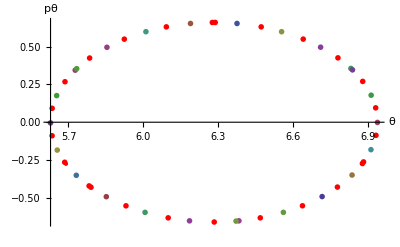

```mathematica
poincarePlot[0.2,1,0.3,50,100,1,5,0]
```